# A Boolean model of geroconversion

Loading the library

```mathematica
$Path = $Path  ∪ {NotebookDirectory[]};
```

```mathematica
<<Booned`
```

#### Transition function

```mathematica
F= {
Insulin-> Insulin,
GF-> GF,
Senescence->  (!p16&& p21&& mTORC1S6K1)||(p16),
G1S->(!p21&& CDK2&& E2F1&& Metabolism),
MAPK -> (GF && !PP2A),
p16 -> (MAPK && !p53 && !E2F1 && !PRC),
MDM2 -> (!p16&&!p53&& AKT&&!mTORC1S6K1&&!MYC&&!E2F1)||(!p16&& p53&&!mTORC1S6K1&&!MYC&&!E2F1)||(p16&&!mTORC1S6K1&&!MYC&&!E2F1),
p53 ->(!MDM2),
p21 ->(!p53&&!AKT&&!MYC&& FOXO)||(p53&&!AKT&&!MYC),
AKT ->(!IRSPIK3CA&&!PTEN&& CDK2&&!PP2A)||(IRSPIK3CA&&!PTEN&&!PP2A),
mTORC1S6K1 -> (!AMPK && !TSC),
ATP -> Metabolism,
IRSPIK3CA -> Insulin,
AMPK -> (p53 && !ATP),
PTEN -> (p53 && !AKT),
TSC -> (!MAPK&&!AKT&& AMPK),
MYC -> (MAPK&&!p53&& mTORC1S6K1&& E2F1),
CDK2 ->(!p21&& mTORC1S6K1&&!MYC&& E2F1)||(!p21&& mTORC1S6K1&& MYC),
RB1 -> (!CDK2),
E2F1 -> (!GF&& MYC&&!RB1&& E2F1)||(GF&&!RB1&& E2F1),
PRC -> (!AKT && MYC),
Metabolism ->(!MAPK&&!AKT&& mTORC1S6K1&& PP1C)||(!MAPK&& AKT&& mTORC1S6K1)|(MAPK&&!AKT&& PP1C)||(MAPK&& AKT),
PP2A -> (!mTORC1S6K1),
FOXO ->(!MAPK&&!p16&&!AKT&&!AMPK&& Metabolism)||(!MAPK&&!p16&&!AKT&& AMPK)||(!MAPK&& p16&&!AKT),
PP1C -> (!MAPK&& AKT)||(MAPK)
};
```

```mathematica
Highlighted@TraditionalForm@TableForm[F]
```

Insulin→Insulin
GF→GF
Senescence→(¬p16∧p21∧mTORC1S6K1)∨p16
G1S→¬p21∧CDK2∧E2F1∧Metabolism
MAPK→GF∧¬PP2A
p16→MAPK∧¬p53∧¬E2F1∧¬PRC
MDM2→(¬p16∧¬p53∧AKT∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(¬p16∧p53∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(p16∧¬mTORC1S6K1∧¬MYC∧¬E2F1)
p53→¬MDM2
p21→(¬p53∧¬AKT∧¬MYC∧FOXO)∨(p53∧¬AKT∧¬MYC)
AKT→(¬IRSPIK3CA∧¬PTEN∧CDK2∧¬PP2A)∨(IRSPIK3CA∧¬PTEN∧¬PP2A)
mTORC1S6K1→¬AMPK∧¬TSC
ATP→Metabolism
IRSPIK3CA→Insulin
AMPK→p53∧¬ATP
PTEN→p53∧¬AKT
TSC→¬MAPK∧¬AKT∧AMPK
MYC→MAPK∧¬p53∧mTORC1S6K1∧E2F1
CDK2→(¬p21∧mTORC1S6K1∧¬MYC∧E2F1)∨(¬p21∧mTORC1S6K1∧MYC)
RB1→¬CDK2
E2F1→(¬GF∧MYC∧¬RB1∧E2F1)∨(GF∧¬RB1∧E2F1)
PRC→¬AKT∧MYC
Metabolism→(¬MAPK∧¬AKT∧mTORC1S6K1∧PP1C)∨(¬MAPK∧AKT∧mTORC1S6K1)|(MAPK∧¬AKT∧PP1C)∨(MAPK∧AKT)
PP2A→¬mTORC1S6K1
FOXO→(¬MAPK∧¬p16∧¬AKT∧¬AMPK∧Metabolism)∨(¬MAPK∧¬p16∧¬AKT∧AMPK)∨(¬MAPK∧p16∧¬AKT)
PP1C→(¬MAPK∧AKT)∨MAPK

The set of variables of the Boolean network.

```mathematica
Keys[F]
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

#### Interaction graph

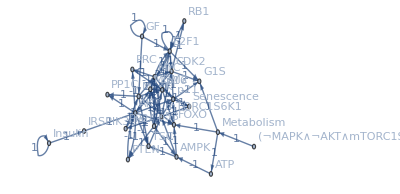

```mathematica
ig0 = InteractionGraphSimple[F]
```

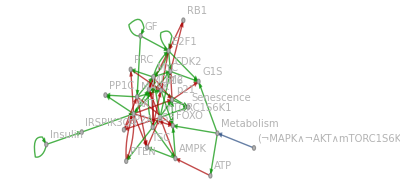

```mathematica
NiceIG[ig0]
```

```mathematica
NiceIG3D[ig0]
```

-Graphics3D-